```mathematica
(*fπ[x_]:=1/2*2.6*x^(0.75-1)(1-x)^0.95+1/6*0.21/Beta[0.5+1,8+1] x^(0.5-1)(1-x)^8
gπ[x_]:=-1/6*0.21/Beta[0.5+1,8+1] x^(0.5-1)(1-x)^8*)
```

```mathematica
Hqz=DiracDelta[x-β-ξ*α]*(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*(1/2*2.6*β^(0.75-1)(1-β)^0.95+1/6*0.21/Beta[0.5+1,8+1] β^(0.5-1)(1-β)^8)/(1-t/λ1^2);
Hqf=DiracDelta[x-β-ξ*α]*(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*(-1/6*0.21/Beta[0.5+1,8+1] Abs[β]^(0.5-1)*(1-Abs[β])^8)/(1-t/λ1^2);
```

```mathematica
Hqfn=Hqf/.{b0->2,ξ->0.3,λ1->0.79,t->-1};
Hqzn=Hqz/.{b0->2,ξ->0.3,λ1->0.79,t->-1};
```

```mathematica
inHf=Assuming[x>-0.3&&x<0.3,Integrate[Hqfn,{β,-1,0},{α,Abs[β]-1,1-Abs[β]}]];
inHz=Assuming[x>-0.3&&x<0.3,Integrate[Hqzn,{β,0,1},{α,Abs[β]-1,1-Abs[β]}]];
```

```mathematica
inHf/.{x->-0.1}
```

-0.711802

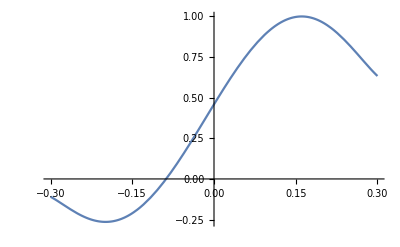

```mathematica
Plot[inHf+inHz,{x,-0.3,0.3}]
```

```mathematica
(*数值计算delta函数版本*)
Hqz1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*(1/2*2.6*β^(0.75-1)(1-β)^0.95+1/6*0.21/Beta[0.5+1,8+1] β^(0.5-1)(1-β)^8)/(1-t/λ1^2);
Hqf1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*(-1/6*0.21/Beta[0.5+1,8+1] Abs[β]^(0.5-1)*(1-Abs[β])^8)/(1-t/λ1^2);
Hqf2=(Hqf1/.{α->(x-β)/ξ})/ξ;
Hqz2=(Hqz1/.{α->(x-β)/ξ})/ξ;
Hqfn2[x_]=Hqf2/.{b0->2,ξ->0.3,λ1->0.79,t->-1};
Hqzn2[x_]=Hqz2/.{b0->2,ξ->0.3,λ1->0.79,t->-1};
```

```mathematica
inHf2[x_]:=Assuming[x>-0.3&&x<0.3,NIntegrate[Hqfn2[x],{β,(x-0.3)/(1+0.3),0}]];
inHz2[x_]:=Assuming[x>-0.3&&x<0.3,NIntegrate[Hqzn2[x],{β,0,(x+0.3)/(1+0.3)}]];
```

```mathematica
inHf2[-0.1]
```

-0.711802